```mathematica
ps1[x_]:=Style[x,Blue,Bold,18]
```

```mathematica
StyledListLinePlot[x_,y_]:=ListLinePlot[x,PlotStyle->{Red,Orange,Darker[Green],Blue},AxesLabel->{ps1["U,V"],ps1["I,uA"]},LabelStyle->Directive[Blue,Bold,FontSize->18],PlotMarkers->{●,15},GridLines->{Range[-1,1,0.1],Range[0,60,5]},PlotLegends->Placed[Table[ps1[y[[i]]],{i,Length[y]}],Above],ImageSize->Full]
```

```mathematica
StyledListLinePlot[x_]:=StyledListLinePlot[x,{ps1["I"],ps1["I_ionic"]}]
```

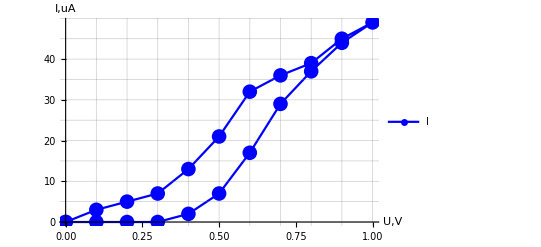

```mathematica
Kz01iv=({{0, 0}, {0.1, 0}, {0.2, 0}, {0.3, 0}, {0.4, 2}, {0.5, 7}, {0.6, 17}, {0.7, 29}, {0.8, 37}, {0.9, 44}, {1, 49}, {0.9, 45}, {0.8, 39}, {0.7, 36}, {0.6, 32}, {0.5, 21}, {0.4, 13}, {0.3, 7}, {0.2, 5}, {0.1, 3}, {0, 0}});StyledListLinePlot[Kz01iv]
```

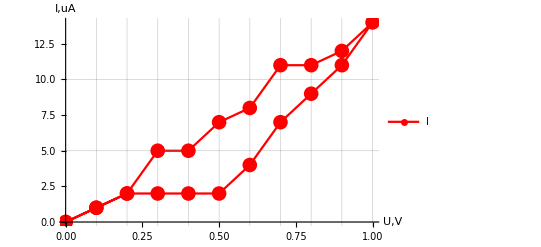

```mathematica
Kz02iv=({{0, 0}, {0.1, 1}, {0.2, 2}, {0.3, 2}, {0.4, 2}, {0.5, 2}, {0.6, 4}, {0.7, 7}, {0.8, 9}, {0.9, 11}, {1, 14}, {0.9, 12}, {0.8, 11}, {0.7, 11}, {0.6, 8}, {0.5, 7}, {0.4, 5}, {0.3, 5}, {0.2, 2}, {0.1, 1}, {0, 0}});StyledListLinePlot[{Kz02iv}]
```

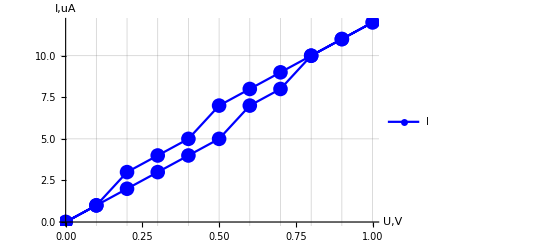

```mathematica
Kz03iv=({{0, 0}, {0.1, 1}, {0.2, 2}, {0.3, 3}, {0.4, 4}, {0.5, 5}, {0.6, 7}, {0.7, 8}, {0.8, 10}, {0.9, 11}, {1, 12}, {0.9, 11}, {0.8, 10}, {0.7, 9}, {0.6, 8}, {0.5, 7}, {0.4, 5}, {0.3, 4}, {0.2, 3}, {0.1, 1}, {0, 0}});StyledListLinePlot[Kz03iv]
```

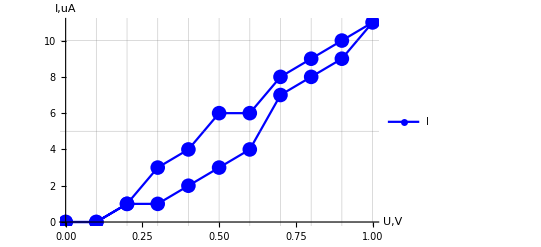

```mathematica
Mz94iv=({{0, 0}, {0.1, 0}, {0.2, 1}, {0.3, 1}, {0.4, 2}, {0.5, 3}, {0.6, 4}, {0.7, 7}, {0.8, 8}, {0.9, 9}, {1, 11}, {0.9, 10}, {0.8, 9}, {0.7, 8}, {0.6, 6}, {0.5, 6}, {0.4, 4}, {0.3, 3}, {0.2, 1}, {0.1, 0}, {0, 0}});StyledListLinePlot[Mz94iv]
```

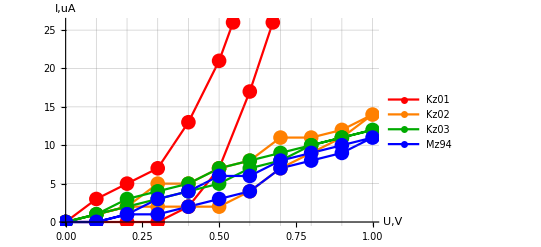

```mathematica
StyledListLinePlot[{Kz01iv,Kz02iv,Kz03iv,Mz94iv},{"Kz01","Kz02","Kz03","Mz94"}]
```